# Explorations: Modules with Random Settlers of Catan Boards Workshop

## Rory Foulger

## Goal: Create a function which generates random boards for Settlers of Catan

Catan is a board game with resource tiles shaped like hexagons, and trading doc tiles shaped like circles. Each tile has a number which dictates who is allowed to collect that resource during that turn.

Catan includes:

19 hexagonal tiles

3 Brick (red)

3 Ore (purple)

4 Wheat (yellow)

4 Wood (dark green)

4 Sheep (light green)

1 Desert (beige)

9 trading docks (circles)

1 to trade two Sheep (light green)

1 to trade two Brick (red)

1 to trade two Wood (dark green)

1 to trade two Ore (purple)

1 to trade two Wheat (yellow)

4 to trade three of any resource (grey)

number allocations for the hexagons

1 number 2

1 number 12

2 of each number 3 -11

Placement rules

Desert doesn’t get a number tile

Each other hexagon must get a number

## Task

Build a random generator which puts the tiles into a random placement and assigns them a random number:

## Code to Use

```mathematica
wheat=RGBColor[Rational[16, 17], Rational[173, 255], 0];
lumber=RGBColor[Rational[27, 85], Rational[25, 51], Rational[5, 51]];
wool=RGBColor[Rational[63, 85], Rational[208, 255], Rational[53, 85]];
ore= RGBColor[Rational[41, 85], Rational[37, 85], Rational[131, 255]];
brick=RGBColor[Rational[52, 85], Rational[67, 255], 0];
blank =  RGBColor[Rational[163, 255], Rational[173, 255], Rational[184, 255]];
desert=RGBColor[Rational[44, 85], Rational[124, 255], Rational[77, 255]];
```

```mathematica
shiptiles =
{(*top two*)
Disk[{-3,9},0.8],
Disk[{3,9},0.8],
(*second line*)
Disk[{9.5,5.5},0.8],
Disk[{-9.5,5.5},0.8],
(*third row*)
Disk[{9.3,-1.9},0.8],
Disk[{-9.3,-1.9},0.8],
(*fourth row*)
Disk[{6.2,-7},0.8],
Disk[{-6.2,-7},0.8],
(*single*)
Disk[{0,-11},0.8]
}
```

```mathematica
rctiles=
{(*far left*)
RegularPolygon[{-7,4},{2,0},6],
RegularPolygon[{-7,0},{2,0},6],
RegularPolygon[{-7,-4},{2,0},6],

(*inner left*)
RegularPolygon[{-3.5,6},{2,0},6],
RegularPolygon[{-3.5,2},{2,0},6],
RegularPolygon[{-3.5,-2},{2,0},6],
RegularPolygon[{-3.5,-6},{2,0},6],

(*center column*)
RegularPolygon[{0,8},{2,0},6],
RegularPolygon[{0,4},{2,0},6],
RegularPolygon[{0,-4},{2,0},6],
RegularPolygon[{0,-8},{2,0},6],
RegularPolygon[{0,0},{2,0},6],

(*inner right*)
RegularPolygon[{3.5,6},{2,0},6],
RegularPolygon[{3.5,2},{2,0},6],
RegularPolygon[{3.5,-2},{2,0},6],
RegularPolygon[{3.5,-6},{2,0},6],

(*far right*)
RegularPolygon[{7,4},{2,0},6],
RegularPolygon[{7,0},{2,0},6],
RegularPolygon[{7,-4},{2,0},6]}
```

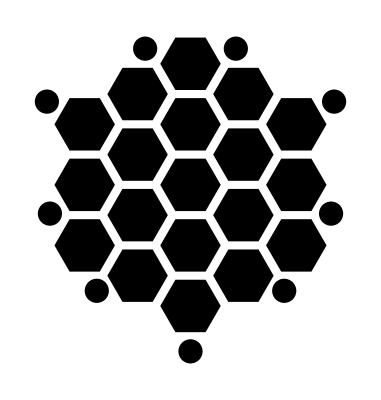

```mathematica
Graphics[{shiptiles, rctiles}]
```

### Need Help? Hint:

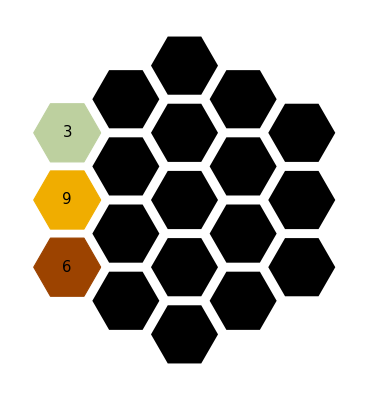

```mathematica
Graphics[{

{EdgeForm[Thickness[Large]],RGBColor[Rational[63, 85], Rational[208, 255], Rational[53, 85]],RegularPolygon[{-7,4},{2,0},6],Inset[3,{-7,4}]},{EdgeForm[Thickness[Large]],RGBColor[Rational[16, 17], Rational[173, 255], 0],RegularPolygon[{-7,0},{2,0},6],Inset[9,{-7,0}]},{EdgeForm[Thickness[Large]],RGBColor[Rational[52, 85], Rational[67, 255], 0],RegularPolygon[{-7,-4},{2,0},6],Inset[6,{-7,-4}]},
(*inner left*)
RegularPolygon[{-3.5,6},{2,0},6],
RegularPolygon[{-3.5,2},{2,0},6],
RegularPolygon[{-3.5,-2},{2,0},6],
RegularPolygon[{-3.5,-6},{2,0},6],

(*center column*)
RegularPolygon[{0,8},{2,0},6],
RegularPolygon[{0,4},{2,0},6],
RegularPolygon[{0,-4},{2,0},6],
RegularPolygon[{0,-8},{2,0},6],
RegularPolygon[{0,0},{2,0},6],

(*inner right*)
RegularPolygon[{3.5,6},{2,0},6],
RegularPolygon[{3.5,2},{2,0},6],
RegularPolygon[{3.5,-2},{2,0},6],
RegularPolygon[{3.5,-6},{2,0},6],

(*far right*)
RegularPolygon[{7,4},{2,0},6],
RegularPolygon[{7,0},{2,0},6],
RegularPolygon[{7,-4},{2,0},6]
}]
```

### Need Help? Hint:

you’ll want to get a random ordering of the tile positions, colors, numbers to inset etc.

To make the tiles appear, you need:

The color

The shape

the number and the position of the tile

you’ll need to find a way to position text within Graphics, look into the function Text or Inset

One approach:

get a list of a random tile color, number, and position

reorganize your lists to fit the order they need for graphics, if needed

Add any extra styling you'd like